```mathematica
data = Import["E:\\GitHub\\bilibili-api\\bilibili-po\\分析\\article-fans.txt","Table"];
```

```mathematica
data=Select[data,#⟦2⟧<500&];
```

```mathematica
article=data⟦;;,2⟧;
```

```mathematica
统计投稿数
```

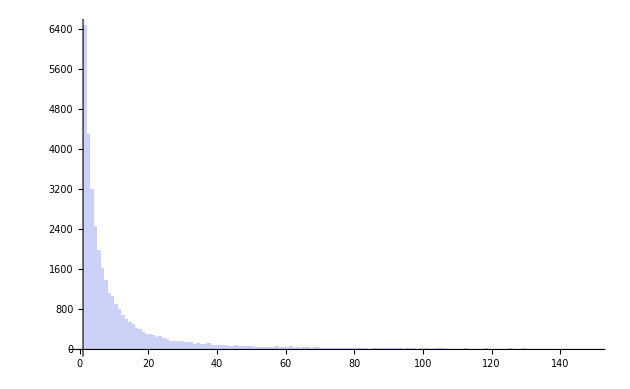

```mathematica
Histogram[Select[article,150> #&],{1}]
```

```mathematica
投稿数大于150的Up人数
```

```mathematica
Select[article,#>150&]//Length
```

571

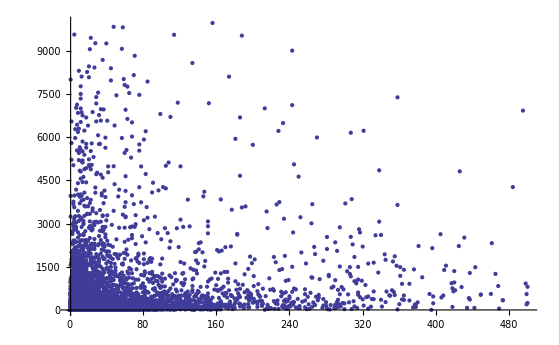

```mathematica
ListPlot[Select[data⟦;;,{2,3}⟧,#⟦2⟧<10000&&#⟦1⟧≤500&],PlotRange->All]
```

```mathematica
不同投稿数的平均好友数
```

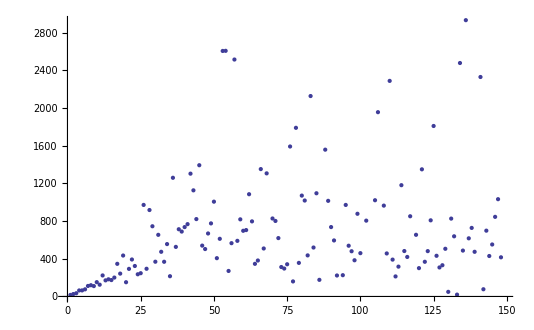

```mathematica
clu = Gather[data⟦;;,{2,3}⟧,#1⟦1⟧==#2⟦1⟧&];
articleFans=SortBy[{#⟦1,1⟧,N@Mean@#⟦;;,2⟧}&/@clu,First];
ListPlot@Select[articleFans,#⟦1⟧<150&]
```

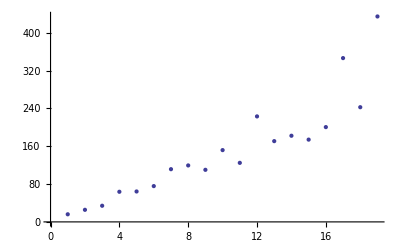

```mathematica
ListPlot@Select[articleFans,#⟦1⟧<20&]
```

```mathematica
每投一稿，平均水平涨17粉
```

```mathematica
FindFit[Select[articleFans,#⟦1⟧<20&],a x+b,{a,b},x]
```

{a→17.3422,b→-22.2525}

```mathematica
ID对应粉丝数
```

```mathematica
idfans = data⟦;;,{1,3}⟧;
```

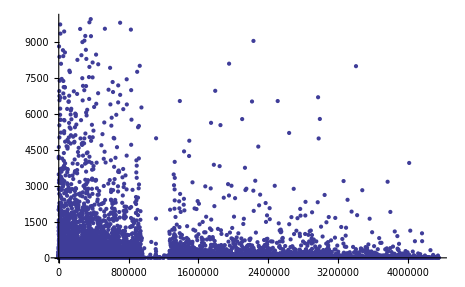

```mathematica
ListPlot[Select[idfans,#⟦2⟧<10000&],PlotRange->All]
```

```mathematica
idarticle = data⟦;;,{1,2}⟧;
```

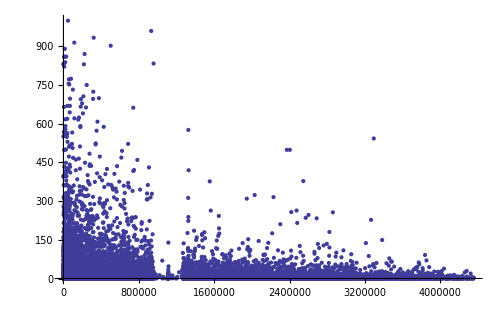

```mathematica
ListPlot[Select[idarticle,#⟦2⟧<1000&],PlotRange->All]
```

```mathematica
不同id段Up主统计
```

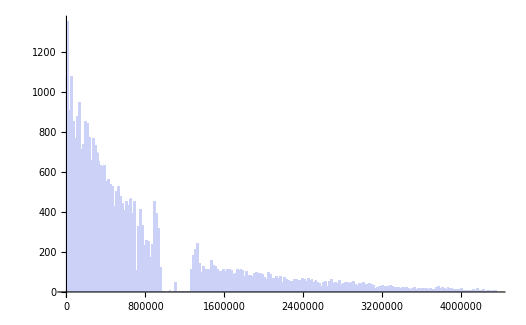

```mathematica
Histogram[data⟦;;,1⟧,200]
```

```mathematica
按ID聚类:
```

```mathematica
k=5000;
idclu = SortBy[Gather[data,Floor[#1⟦1⟧/k]==Floor[#2⟦1⟧/k]&],First];
idMeanArticle={#⟦1,1⟧,N@Mean@#⟦;;,2⟧}&/@idclu;
idMeanFans={#⟦1,1⟧,N@Mean@#⟦;;,3⟧}&/@idclu;
idMeanNumber={#⟦1,1⟧,N@Length@#}&/@idclu;
```

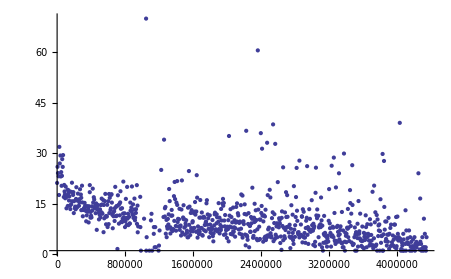

```mathematica
ListPlot[idMeanArticle,PlotRange->All]
```

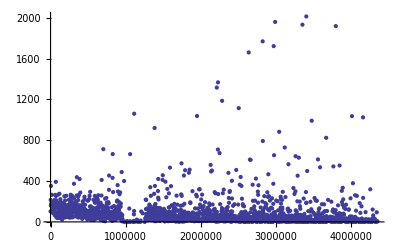

```mathematica
ListPlot[Select[idMeanFans,#⟦2⟧<10000&],PlotRange->All]
```

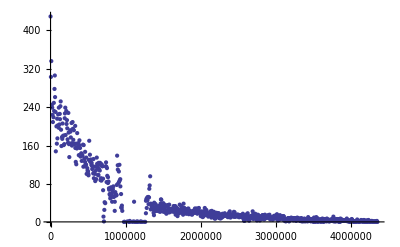

```mathematica
ListPlot[idMeanNumber,PlotRange->All]
```

```mathematica
关注关系网
```

```mathematica
forelation = Import["E:\\GitHub\\bilibili-api\\bilibili-po\\分析\\up-follow.txt","Table",CharacterEncoding->"UTF8"];
```

```mathematica
upinfp =  Import["E:\\GitHub\\bilibili-api\\bilibili-po\\分析\\upinfo.txt","Table",CharacterEncoding->"UTF8"];
upinfp={#⟦1⟧,StringJoin[#⟦2;;⟧]}&/@upinfp//Quiet;
```

```mathematica
(*根据up的id获取用户名*)
GetUp[id_]:=Select[upinfp,#⟦1⟧==id&]⟦1⟧⟦2⟧;
```

```mathematica
cor = Select[forelation,#⟦3⟧==2&];
cor = cor⟦;;,1;;2⟧;
cor = Thread[cor⟦;;,1⟧<->cor⟦;;,2⟧];
```

```mathematica
g=Graph@cor
```

-Graphics-

```mathematica
connectcomponent = ConnectedComponents[g];
```

```mathematica
connectcomponent⟦1⟧//Length
```

10518

```mathematica
Select[connectcomponent,Length@#==2&]//Length
```

1155

```mathematica
subgraph = Subgraph[g,connectcomponent⟦1⟧]
```

-Graphics-

```mathematica
VertexDegree[subgraph]//Max
```

142

```mathematica
degreetable = Table[{VertexList[subgraph]⟦i⟧,VertexDegree[subgraph]⟦i⟧},{i,1,Length@VertexList[subgraph]}];
```

```mathematica
GetUp@#&/@(SortBy[degreetable,Last]⟦-100;;⟧⟦;;,1⟧)//Reverse
```

{oeasy,Azure冰梦,ふらわ~,Dove♪神痕灬,雪洒竹林,Magus,阿燐酱,incub8or,96猫＠141.2cm,掌心の羁绊,莫非命,Lucky好心情,Tio.Nyaruko,meiling,Aru,SonicoQ,SuperBrother,抠脚黑汉子,头顶小胖次,白羽沉,オルゴール,珠峰喵,FATE零零七,她,新华里业务员,にししししー,复仇女王,wearsky,小伞一把,佐仓•M•沙耶加,西方良目仙人掌,傲娇麒儿,LOKO&洛可,ここにいるよ,luckAMV,西行寺·爱多多姐,Caaaaarrot,Z·DARK,新堂爱卖萌,小然参上,泰德【Ted】,Gintoki_JF,M.Scarlet,恋之八卦炉,妄想世界協會,人生赢家小明,杂菌,Falling捏捏,深海庞贝,橘丶万里花酱,Mr甜点,何满子,AME_AOI,松江府人,可爱Baby猫,小小☆精灵,哈露ちゃん,真鱼,fumo,谈情不说爱,Xmyz.G,小帅喵,李仙缘,小透明BAKA,特莱嘻嘻嘻,烤夜雀,天蓝梦境,二米明子,望天晓,樱鸠十六夜,77323xd43,DigiCat,东城绫的忧郁,冰水地缚灵,以太,LAM1992,☆来来子,XiaoLLK,☆玉玉子,Shepherd小牧,柚小悶,发癫的四叶草,诶姆,兰豆子,CRAZY262,世界の敌,本多二代二代TF,毛毛菌殿下,xkd青鱼,Smithy铁匠,JUSF,正经战队,小白Pikiyo,純白,20024JoK,雪丿下雪乃,白white饭,vertigo,南云霞丶,CC子}

```mathematica
mindegree = 15;
filterup = Select[degreetable,#⟦2⟧≥mindegree&];
maingrap = Subgraph[subgraph,filterup⟦;;,1⟧];
maingrap=Subgraph[maingrap,ConnectedComponents[maingrap]⟦1⟧]
```

-Graphics-

```mathematica
HighlighVertexDegree[g_, vd_]:=HighlightGraph[g,Table[Style[VertexList[g]⟦i⟧,ColorData["TemperatureMap"][vd⟦i⟧/Max[vd]]],{i,VertexCount[g]}]];
```

```mathematica
HighlighVertexDegree[maingrap,VertexDegree[maingrap]]
```

-Graphics-

```mathematica
namelist = {#->GetUp@#}&/@VertexList[maingrap]//Flatten;
```

```mathematica
Graph[EdgeRules[maingrap],DirectedEdges->False,VertexLabels->namelist]
```

-Graphics-

```mathematica
最大完全图
```

```mathematica
GetUp@#&/@FindClique[g]⟦1⟧
```

{白羽沉,CC子,Magus,96猫＠141.2cm,ビリくん,小透明BAKA,兰豆子,她,寂寞的傲娇}